```mathematica
n=W*hbar*w0^3*tau/(Pi^2*c^2);
```

```mathematica
numbers={W->1/60,
hbar->1.05457182×10^(-34),
w0->2*Pi*(3*10^8)/(590*10^(-9)),
e0->8.858*10^(-12),
c->3*10^8,
tau->16*10^(-9),
kB->1.380649×10^(-23)};
```

```mathematica
n/.numbers
```

1.0324×10^-15

```mathematica
Solve[n==1/(Exp[hbar*w0/(kB*T)]-1),T]/.numbers
```

{{T→ConditionalExpression[24402.9/(34.5069+2 ⅈ π C[1]), C[1]∈ℤ]}}

```mathematica
24402.93093599141/34.50688565171109
```

707.19

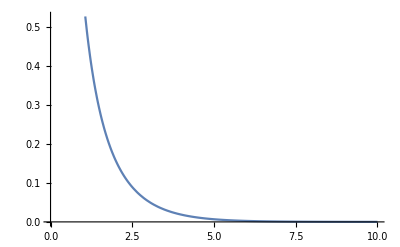

```mathematica
Plot[1/(Exp[x]-1),{x,0,10}]
```

```mathematica
g0=4*o^3*(e*a0)^2/(3*Pi*hbar*c^3);
```

```mathematica
num2={o->2*Pi*(3*10^8)/(21*10^(-2)),
muB->9.27400999×10^(-24),
e0->8.858*10^(-12),
hbar->1.05457182×10^(-34),
c->3*10^8,
e->1.602*10^(-19),
a0->0.529*10^(-10)};
```

```mathematica
g0*(1/137)^2/.num2
```

1.16411×10^-14

```mathematica
1/(g0*(1/137)^2)/.num2
```

8.59025×10^13

```mathematica
(*convert seconds to years*)
```

```mathematica
(8.590254116088494*^13)/(365*24*60*60)
```

2.72395×10^6